# GMRES Generalized Minimum Residual

We are going to iteratively approximate the solution of 
	A.x=b
using the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
The polynomial 
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1) 
(remember x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b) is going to make another appearance and the target x_exact=A^-1.b satisfies A.x_exact=b.

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Q_n is an orthogonal basis for the something approximating the “large” eigenspace of A

Q_(n+1)=[Q_n|q_(n+1)]

By construction multiplying by A maps 𝒦_n→𝒦_(n+1) and the map is expressed by H_n

H_n=((Ĥ)_n
0,…,0,H_(n+1,n)) is a rectangular Hessenberg matrix.

## GMRES

The GMRES approximation is simply
	x_n=argmin_(x∈𝒦_n)||A.x-b||
We have a convenient basis for 𝒦_n so we write x_n=Q_n.y_n and note that
	y_n=argmin_(y∈ℝ^n)||A.Q_n.y-b||=argmin_y||Q_(n+1).H_n.y-b||
In words, y_n is the best solution in 𝒦_n and the Arnoldi construction lets us explicitly flip things into the one larger space. We are nearly done remember b∈𝒦_(n+1) and (Q_(n+1))ᵀ.b=e_1 and Q_(n+1) is orthogonal so
		y_n=argmin_y||Q_(n+1).H_n.y-b||=argmin_y||H_n.y-(Q_(n+1))ᵀ.b||=argmin_y||H_n.y-||b||e_1||
The last problem is a small linear least squares problem with an almost triangular right hand side.

Since we already have Arnoldi code this will be pretty easy to code.

The question is how fast does it converge?

The residuals r_n=b-A.x_n satisfy
	||r_n||=min_(x∈𝒦_n) ||A.x-b||=min_(y∈ℝ^n) ||H_n.y-||b||e_1||

||r_(n+1)||≤||r_n|| since 𝒦_(n+1)⊃𝒦_n.

The residuals are given by polynomials in A i.e.
	x_n=(c_1 A^0+c_2 A^1+…+c_n A^(n-1)).b

r_n=b-A.x_n=(I_m-A.(c_1 A^0+c_2 A^1+…+c_n A^(n-1))).b

By definition, GMRES produces best optimal polynomial in the space 𝒫_n^GMRES={1+a_1 z+…+a_n z^n}.

p_n^GMRES=argmin_(p∈𝒫_n^GMRES)|| p(A).b||

Since we run out of dimensions when n=m we know that r_m=0.

The induced matrix norm satisfies ||p(A).b||≤||p(A)(||)_induced||b|| for any polynomial. So we have

(||r_n||)/(||b||)=(||p_n^GMRES(A).b||)/(||b||)≤(||p(A).b||)/(||b||)≤||p(A)(||)_induced  for any p∈𝒫_n^GMRES

If A lets us pick polynomials p∈𝒫_n^GMRES with p(A) small then we know the residuals get small fast.

We are going to come back to this once we see the GMRES in action.

In words, the scaled residual is less than the absolute value of any appropriate polynomial on the spectrum!

Think about what would let us pick a "good" polynomial on the spectra.

## GMRES in Action.

Here is a test matrix with some obvious structure.

```mathematica
m=123; ϵ=3.0;
A=ϵ RandomReal[{-1,1},{m,m}]+DiagonalMatrix[Range[1,m]];
b=RandomReal[{-1,1},m];
xMma=LinearSolve[A,b];
MatrixPlot[A];
MaxIter=60;
bNorm=Norm[b];
{Q,H}={{b/bNorm}ᵀ,{{}}};
xData=Table[
{Q,H}=Arnoldi[A][{Q,H}];
y=LeastSquares[H,SparseArray[1->bNorm,Length[H]]];
x=Q⟦All,1;;-2⟧.y,
{MaxIter}];
rData=Map[Norm[A.#-b]&,xData];
dData=Map[Norm[#-xMma]&,xData];
TabView[{
"rData"->ListLogPlot[rData,Frame->True],
"xData"->MatrixPlot[xData],
"dData"->ListLogPlot[dData,Frame->True],
"r&dData"->ListLogPlot[{rData,dData},Frame->True,
PlotLegends->{"r","d"}]}]
```

1234

It is fairly clear that in some sense the big part of the matrix is diagonal and very simple. We can invert Diagonal matrices very easily.  Look at the spectra of the matrices below.

```mathematica
M=DiagonalMatrix[Diagonal[A]];
TabView[{
"Λ(A)"-> ListPlot[ReIm[Eigenvalues[A]],
PlotRange->All,AspectRatio->Automatic,
Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1.0]}],
"Λ(M^-1.A)"-> ListPlot[ReIm[Eigenvalues[Inverse[M]. A]],
PlotRange->All,AspectRatio->Automatic,
Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1.0]}]
}]
```

12

Why would this help? Well if M is invertible 
	A.x=b ⟺M^-1.A.x=M^-1.b
We can run GMRES on the “preconditioned” system if M^-1.A is a nicer matrix!  It seems to be a much nicer matrix!

```mathematica
MaxIter=60;
M=Inverse[DiagonalMatrix[Diagonal[A]]];
bNew=M.b;
bNewNorm=Norm[bNew];
ANew=M.A;
{Q,H}={{bNew/bNewNorm}ᵀ,{{}}};
xData=Table[
{Q,H}=Arnoldi[ANew][{Q,H}];
y=LeastSquares[H,SparseArray[1->bNewNorm,Length[H]]];
x=Q⟦All,1;;-2⟧.y,
{MaxIter}];
rData=Map[Norm[ANew.#-bNew]&,xData];
dData=Map[Norm[#-xMma]&,xData];
TabView[{
"rData"->ListLogPlot[rData,Frame->True],
"xData"->MatrixPlot[xData],
"dData"->ListLogPlot[dData,Frame->True],
"r&dData"->ListLogPlot[{rData,dData},Frame->True,
PlotLegends->{"r","d"}]}]
```

1234

In practice “preconditioning” is essential for all iterative solvers.  The simplest strategy of just taking the diagonal is called a Jacobi preconditioner. This may help if the matrix has a chunky diagonal.  The usual target for the preconditioner M is to have M≈A^-1 which should cluster eigenvalues of M.A near 1.

## ILU Preconditioners

Lets look at some of this for a familiar matrix.  I added an Identity matrix because the original matrix has zeros on the diagonal!

SparseArray[<131430>, {4241, 4241}]

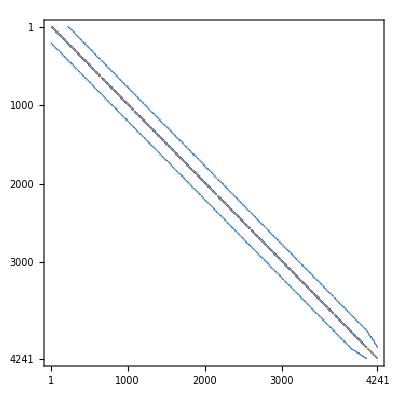

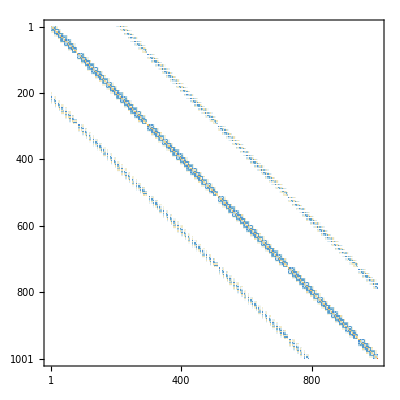

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/drivcav/e20r0100.mtx.gz"]
MatrixPlot[A]
MatrixPlot[A⟦1000;;2000,1000;;2000⟧]
m=Length[A];
A=A+SparseArray[Band[{1,1}]->1.0,{m,m}];
```

Here is the spectrum and the Jacobi preconditioned spectrum. The Jacobi preconditioned spectrum is better but not great.

```mathematica
λs=Eigenvalues[A];
jM=Inverse[DiagonalMatrix[Normal[Diagonal[A]]]];
jλs=Eigenvalues[jM.A];
TabView[{
"Λ(A)"->ListPlot[ReIm[λs],PlotRange->All,Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1.0]}],
"Λ(jM.A)"->ListPlot[ReIm[jλs],PlotRange->All,Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},1.0]}]
}]
```

Eigenvalues::arh: Because finding 4241 out of the 4241 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

12

There are standard modifications to LU decompositions for sparse matrices that go by ILU for Incomplete LU decompositions that can produce better preconditioners.  The idea is to just limit the fill-in an LU decomposition does by stopping before you are finished!  This is not as crazy as it sounds!  Mathematica has a built in but undocumented ILU command. Here is a picture of the output.

```mathematica
m=Length[A];
{LU,piv,cond}=LUDecomposition[A];
{ILU,Ipiv}=SparseArray`SparseMatrixILU[A];
{U,IU} = Map[UpperTriangularize,{LU,ILU}];
{L,IL}=Map[
LowerTriangularize[#,-1]+SparseArray[Band[{1,1}]->1,{m,m}]&,
{LU,ILU}];
TabView[{
"A"->MatrixPlot[A],
"L"->MatrixPlot[L],
"U"->MatrixPlot[U],
"IL"->MatrixPlot[IL],
"IU"->MatrixPlot[IU]
}]
```

12345

The ILU decomposition is an approximation to the LU decomposition.

```mathematica
{Norm[L.U-A,"Frobenius"],Norm[IL.IU-A,"Frobenius"]}/Norm[A,"Frobenius"]
```

{1.29435×10^-16,0.002091}

Of course, the point of an LU decomposition is to build a simple way to compute 
	A^-1.b=(L.U)^-1.b=U^-1.(L^-1.b)
This works because A^-1=U^-1.L^-1 An ILU only satisfies A^-1≈(IU)^-1.(IL)^-1. Of course, what we really care about is if the eigenvalues are more clustered!

```mathematica
ILInvA=Inverse[Normal[IU]].Inverse[Normal[IL]].Normal[A];
Norm[ILInvA-IdentityMatrix[m],"Frobenius"]/Norm[A,"Frobenius"]
ILUλs=Eigenvalues[ILInvA];
TabView[{
"Λ(A)"->ListPlot[ReIm[λs],PlotRange->All],
"Λ(jM.A)"->ListPlot[ReIm[jλs],PlotRange->All],
"Λ_ILU"->ListPlot[ReIm[ILUλs],PlotRange->All,
Prolog->{LightGreen,EdgeForm[Red],Disk[{1,0},0.007]}]
}]
```

0.000527171

123

Since all the eigenvalues of the ILU preconditioned matrix are inside the disk of radius 0.007 if we choose the polynomial p(z)=(1-z)^n we see that 
	r_n/||b||≤C (0.007)^n-
where C is the condition number of the eigenvector matrix.

As promised!

```mathematica
MaxIter=12;
ρ=0.007;
xMma=RandomReal[{-1,1},Length[ILInvA]];
b=ILInvA.xMma;
{Q,H}={{b/Norm[b]}ᵀ,{{}}};
xData=Table[
{Q,H}=Arnoldi[ILInvA][{Q,H}];
y=LeastSquares[H,SparseArray[1->Norm[b],Length[H]]];
x=Q⟦All,1;;-2⟧.y,
{MaxIter}];
rData=Map[Norm[ILInvA.#-b]&,xData];
dData=Map[Norm[#-xMma]&,xData];
TabView[{
"rData"->ListLogPlot[rData,Frame->True],
"xData"->MatrixPlot[xData],
"dData"->ListLogPlot[dData,Frame->True],
"r&dData"->ListLogPlot[{rData,dData,Table[ ρ^n,{n,1, MaxIter}]},Frame->True,
PlotLegends->{"r","d","err"}]}]
```

1234